## Project Description

Project Authors: Nicholas Handelman and Shreyas Shanbhag
Reference Paper: Portfolio selection with a drawdown constraint (2006, Gordon J. Alexander and Alexandre M. Baptista)
	    URL:	     https://www.sciencedirect.com/science/article/pii/S0378426606001312
	    Appendix: http://home.gwu.edu/~alexbapt/JBFAppendix.pdf

In this project, we implement the various models described in the reference paper. First, we gather and prepare the data used in the paper. Next we implement the models and discuss the results.

## Global Parameters

```mathematica
(*Include trailing backslash \*)
sDataFolder="Index Standard (Large+Mid) 1970-2004\\";
```

## Prepare Index Returns Data

MSCI Index monthly price data from their website (https://www.msci.com/end-of-day-data-search). Only need to keep December data for each year. Convert price data to yearly return data. Save as Mathematica .m file for reuse.

### Load, Clean and Save XLS Price Data from MSCI

```mathematica
xLoadData[sFileName_]:=Block[{vvData},
vvData=Import[NotebookDirectory[]<>sFileName][[1]];
Select[vvData,DateObjectQ[#[[1]]]==True&&#[[1]]["Month"]==12&]
]

If[False,
vIndexNames=FileNames[sDataFolder<>"*.xls"];
vvIndexPricesData=Map[xLoadData[#]&,vIndexNames];
vIndexNames=Map[StringDelete[#," Index.xls"]&,vIndexNames];
vIndexNames=Map[StringDelete[#,sDataFolder]&,vIndexNames];

SetDirectory[NotebookDirectory[]];
Export[sDataFolder<>"Indexes Yearly Prices.m",{vIndexNames,vvIndexPricesData}];
]
```

### Load Cleaned Price Data, Convert to Yearly Returns and Save

```mathematica
If[False,
{vIndexNames,vvIndexPricesData}=Import[NotebookDirectory[]<>sDataFolder<>"Indexes Yearly Prices.m"];
vvIndexReturnsData=Map[Transpose@{Rest[#[[All,1]]],Differences[#[[All,2]]]/Most[#[[All,2]]]}&,vvIndexPricesData];

SetDirectory[NotebookDirectory[]];
Export[sDataFolder<>"Indexes Yearly Returns.m",{vIndexNames,vvIndexReturnsData}];
]
```

## Portfolio Optimization

### Section Parameters

```mathematica
nMinER=0.01;
nMaxER=0.2;
nStepsER=0.01;
nRiskFreeRate=0.0275;
vWeightsBench={0,0,.1,.1,0,.2,0,0,.2,.4};
vMaxDDMVCons={.12,.14,.16};
vMaxDDMTEVCons={.05,.06,.07};
```

### Section Variables

#### Load Yearly Returns and Prices

```mathematica
{vIndexNames,vvIndexReturnsTS}=Import[NotebookDirectory[]<>sDataFolder<>"Indexes Yearly Returns.m"];
{vIndexNames,vvIndexPricesTS}=Import[NotebookDirectory[]<>sDataFolder<>"Indexes Yearly Prices.m"];
```

#### Common Variables

```mathematica
vvIndexReturns=vvIndexReturnsTS[[All,All,2]];
vvYearlyReturns=Transpose@vvIndexReturns;
vvIndexPrices=vvIndexPricesTS[[All,All,2]];
iIndexes=Length@vIndexNames;
iStates=Length@vvIndexReturns[[1]];
vvYearlyReturnsRF=Transpose@Append[vvIndexReturns,Table[nRiskFreeRate,iStates]];
{vMeans,vStdDevs}=Transpose@Map[{Mean[#],StandardDeviation[#]}&,vvIndexReturns];
vvVarCovMatrix=Covariance[vvYearlyReturns];
vvVarCovInvMatrix=Inverse[vvVarCovMatrix];

vUnit=Table[1,iIndexes];
nA=vUnit.vvVarCovInvMatrix.vMeans;
nB=vMeans.vvVarCovInvMatrix.vMeans;
nC=vUnit.vvVarCovInvMatrix.vUnit;
nD=nB*nC-nA^2;
vWeightsσ=vvVarCovInvMatrix.vUnit/nC;
vWeightsBA=vvVarCovInvMatrix.vMeans/nA;
vWeightsRF=Append[Table[0,iIndexes],1];
vWeightsTangent=Append[(vvVarCovInvMatrix.(vMeans-vUnit*nRiskFreeRate))/(nA-nC*nRiskFreeRate),0];
nTangentPortER=Append[vMeans,0].vWeightsTangent;
nBenchPortER=vWeightsBench.vMeans;
vRiskFreePort={0,nRiskFreeRate,vWeightsRF};
```

### Section Functions

```mathematica
xMVPoints[vEffPorts_,sLabel_]:=Block[{},
Map[Tooltip[#[[1;;2]],sLabel<>ToString@#[[1;;3]]]&,vEffPorts]
]

xMTEVPoints[vEffPorts_,sLabel_]:=Block[{},
Map[Tooltip[#[[{4,2}]],sLabel<>ToString@#[[{4,2,3,1}]]]&,vEffPorts]
]

xFundSepPoints[vFundSeps_]:=Block[{},
Transpose@Map[{Tooltip[#[[{1,3}]],#[[{1,3}]]],Tooltip[#[[{2,3}]],#[[{2,3}]]]}&,vFundSeps]
]

(*Remove portfolios with infinite variance (i.e. not feasible) and return portfolios sorted by expected return.*)
xFeasiblePorts[vPorts_]:=Block[{},
Sort[Select[vPorts,0≤#[[1]]<Infinity&],#1[[2]]<#2[[2]]&]
]

(*
two side by side plots. Both plots are mix of list line plots and list plots.;
vvListLinePlotData: vector of 2 vectors. first vector has boundary plot data. second vector has frontier plot data.;
vvListPlotData: vector of 2 vectors. first vector has boundary points data. second vector has frontier points data.;
vvPlotLabels: vector of 2 strings. the strings are the labels for each plot;
vAxesLabels: vector of 2 strings. x-axis and y-axis label for both plots.;
vPlotColors: vector of colors for the list line plots;
vLegends: vector strings for list line plot legend values;
*)
xBoundaryFrontierPlots[vvListLinePlotData_,vvListPlotData_,vvPlotLabels_,vAxesLabels_,vPlotColors_,vLegends_]:=Block[{},
Row[{
Show[ListLinePlot[vvListLinePlotData[[1]],PlotRange->{{0,0.4},{0,0.2}},PlotMarkers->Automatic,PlotLegends->Placed[vLegends,Below],PlotStyle->vPlotColors],
ListPlot[vvListPlotData[[1]],PlotRange->{{0,0.4},{0,0.2}},PlotStyle->Directive[PointSize->Large,Black]],
ImageSize->{400,400},PlotLabel->vvPlotLabels[[1]],AxesLabel->vAxesLabels
],"           ",
Show[ListLinePlot[vvListLinePlotData[[2]],PlotRange->{{0,0.4},{0,0.2}},PlotMarkers->Automatic,PlotLegends->Placed[vLegends,Below],PlotStyle->vPlotColors],
ListPlot[vvListPlotData[[2]],PlotRange->{{0,0.4},{0,0.2}},PlotStyle->Directive[PointSize->Large,Black]],
ImageSize->{400,400},PlotLabel->vvPlotLabels[[2]],AxesLabel->vAxesLabels,PlotRange->{{0,0.4},{0,0.2}}
]
}]
]

xFundSepsPlots[vvFundSepPoints_,vvPlotLabels_,vXRange_]:=Block[{},
Row[{
ListStepPlot[vvFundSepPoints[[1]],PlotMarkers->Automatic,PlotLabel->vvPlotLabels[[1]],AxesLabel->{"K","E"},PlotRange->{{0,15},{0,.2}},ImageSize->{400,400}],"           ",
ListLinePlot[vvFundSepPoints[[2]],PlotMarkers->Automatic,PlotLabel->vvPlotLabels[[2]],AxesLabel->{"Sum of Weights","E"},PlotRange->{vXRange,{0,.2}},ImageSize->{400,400}]
}]
]
```

### Display Basic Statistics

Means, Standard Deviations and Correlation Matrix. If you compare these to the calculations in the paper, you can see that the means are all lower. We are not sure why there is a difference. The standard deviations and correlations are closer.

```mathematica
Grid[Prepend[Transpose@Prepend[Transpose@{vIndexNames,Round[vMeans*100,0.01],Round[vStdDevs*100,0.01]},{Null,"Mean %","StdDev %"}],{sDataFolder,SpanFromLeft}],Dividers->All,Alignment->Left]

Grid[Prepend[Prepend[Transpose@Prepend[Round[Correlation[vvYearlyReturns],0.01],vIndexNames],Prepend[vIndexNames,Null]],{"Correlation Matrix: "<>sDataFolder,SpanFromLeft}],Dividers->All,Alignment->Left]
```

Index Standard (Large+Mid) 1970-2004\ |  |  |  |  |  |  |  |  |  | 
 | Australia | Canada | France | Germany | Italy | Japan | Netherlands | Switzerland | UK | USA
Mean % | 7.67 | 8.57 | 11.21 | 11. | 9.59 | 14.29 | 10.1 | 12.32 | 10.51 | 8.59
StdDev % | 23.92 | 19.49 | 27.98 | 29.91 | 36.62 | 34.91 | 18.63 | 24.5 | 27.12 | 17.06

Correlation Matrix: Index Standard (Large+Mid) 1970-2004\ |  |  |  |  |  |  |  |  |  | 
 | Australia | Canada | France | Germany | Italy | Japan | Netherlands | Switzerland | UK | USA
Australia | 1. | 0.68 | 0.63 | 0.36 | 0.5 | 0.48 | 0.62 | 0.38 | 0.59 | 0.52
Canada | 0.68 | 1. | 0.52 | 0.35 | 0.32 | 0.44 | 0.54 | 0.31 | 0.41 | 0.61
France | 0.63 | 0.52 | 1. | 0.75 | 0.75 | 0.5 | 0.81 | 0.7 | 0.5 | 0.56
Germany | 0.36 | 0.35 | 0.75 | 1. | 0.65 | 0.38 | 0.77 | 0.86 | 0.45 | 0.53
Italy | 0.5 | 0.32 | 0.75 | 0.65 | 1. | 0.43 | 0.62 | 0.61 | 0.33 | 0.43
Japan | 0.48 | 0.44 | 0.5 | 0.38 | 0.43 | 1. | 0.44 | 0.32 | 0.31 | 0.3
Netherlands | 0.62 | 0.54 | 0.81 | 0.77 | 0.62 | 0.44 | 1. | 0.82 | 0.67 | 0.78
Switzerland | 0.38 | 0.31 | 0.7 | 0.86 | 0.61 | 0.32 | 0.82 | 1. | 0.57 | 0.58
UK | 0.59 | 0.41 | 0.5 | 0.45 | 0.33 | 0.31 | 0.67 | 0.57 | 1. | 0.6
USA | 0.52 | 0.61 | 0.56 | 0.53 | 0.43 | 0.3 | 0.78 | 0.58 | 0.6 | 1.

### Mean-Variance Optimization - Unconstrained without Risk Free Security

a = 1^T Σ^-1 μ     |     b=μ^T Σ^-1 μ     |     c=1^T Σ^-1 1     |     w_σ=(Σ^-1 1)/c     |     w_a=(Σ^-1 μ)/a     |     ϕ=(E-b/a)/(a/c-b/a)     |     w_E=ϕw_σ+(1-ϕ)w_a
Minimum-Variance portfolio: w_σ, has expected return a/c and variance 1/c
B/A Portfolio: w_a, has expected return b/a
Short sales are allowed, so a closed-form solution exists and is used to find the Mean-Variance efficient boundary: σ(r_w)=1/c+(E[r_w]-a/c)^2/(d/c)

Efficient portfolios on this boundary in (E[r_w],σ[r_w]) space exhibit two-fund separation. The first fund is the minimum variance portfolio. The second fund is the B/A portfolio.

The efficient frontier includes the portfolios on this boundary with E[r_w]≥a/c.

Efficiency loss (in variance or SD units). This is the difference between the variance (or SD) of different boundaries (e.g. unconstrained and constrained).

#### Parameters and Functions

```mathematica
(*Optimization function. Return standard deviation, expected return and weights of efficient portfolio with given expected return*)
xMVONoConsNoRF[nEffER_]:=Block[{nWeightϕ},
nWeightϕ=(nEffER-nB/nA)/(nA/nC-nB/nA);
{Sqrt[1/nC+(nEffER-nA/nC)^2/(nD/nC)],nEffER,nWeightϕ*vWeightsσ+(1-nWeightϕ)*vWeightsBA}
]
```

#### Compute and Display Efficient Boundary and Efficient Frontier

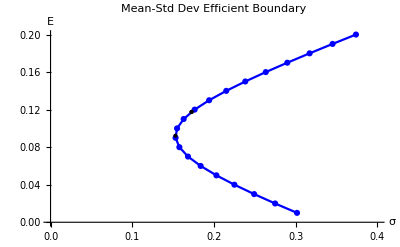
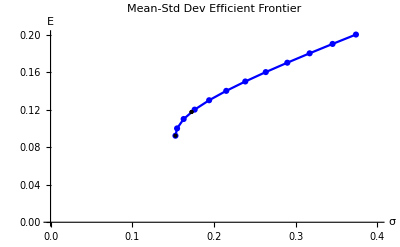

```mathematica
vMVMinVarPort=xMVONoConsNoRF[nA/nC];
vMVBAPort=xMVONoConsNoRF[nB/nA];
vMVEffBoundaryPorts=Table[xMVONoConsNoRF[nEffER],{nEffER,nMinER,nMaxER,nStepsER}];
vMVEffFrontierPorts=Prepend[Select[vMVEffBoundaryPorts,#[[2]]>vMVMinVarPort[[2]]&],vMVMinVarPort];

vMVEffBoundaryPoints=xMVPoints[vMVEffBoundaryPorts,""];
vMVEffFrontierPoints=xMVPoints[vMVEffFrontierPorts,""];
vMVTwoFundPoints=Join[xMVPoints[{vMVMinVarPort},"Min Var Portfolio\n"],xMVPoints[{vMVBAPort},"B/A Portfolio\n"]];

xBoundaryFrontierPlots[
{{vMVEffBoundaryPoints},{vMVEffFrontierPoints}},
{{vMVTwoFundPoints},{vMVTwoFundPoints}},
{"Mean-Std Dev Efficient Boundary","Mean-Std Dev Efficient Frontier"},
{"σ","E"},
{Blue},
{}
]
```

### Mean-Variance Optimization - Maximum Drawdown Constrained without Risk Free Security

S = # of states     |     K = # states bound by MD constraint     |     S_k = bound states
r_s_k=return at s_k     |     D = Max Drawdown Constraint
e_s_k=1^T Σ^-1 r_s_k     |     w_s_k=(Σ^-1 r_s_k)/e_s_k     |     A_(E,D)= [1  E  -D  ...  -D]     |     M = [1  μ  r_s_3 ...  r_(s_(K+2))]
N=M^T Σ^-1 M     |     [λ_1  λ_2  λ_3... λ_(K+2)] = N^-1 A_(E,D)     
[ϕ_1ϕ_2ϕ_3... ϕ_(K+2)] = [λ_1 c  λ_2 a  λ_3 e_s_3... λ_(K+2)e_(s_(K+2))]     |     w_(E,D)=ϕ_1 w_σ+ϕ_2 w_a+ ∑_(k=3)^(K+2) ϕ_k w_s_k
Maximum Drawdown: D[r_w]=-min_(s∈{1,...,S})w^T r_s

A closed-form solution does not exist to find the constrained Mean-Variance efficient boundary. Mathematica’s NMinimize function is capable of solving the vectorized quadratic objective function with 2+S linear constraints. It uses the Nelder-Mead numerical method. 
The program is given as follows: min_w w^T Σw    
s.t.     w^T1=1, 
	w^T μ =E, 
	-w^T r_s≤D  ∀s∈{1,...,S} 

Efficient portfolios on this boundary in (E[r_w],σ[r_w]) space exhibit K+2-fund separation. The first two funds w_σ and w_a are the same efficient funds from the unconstrained optimization. The remaining K funds are unconstrained mean-variance inefficient funds.

The efficient frontier includes the portfolios on this boundary with E[r_w]≥a/c.

#### Functions

```mathematica
xMVOMDConsNoRF[nEffER_,nMaxDD_]:=Block[{vWeights,vResult},
vWeights=Table[ToExpression["w"<>ToString@i],{i,iIndexes}];
vResult=NMinimize[{vWeights.vvVarCovMatrix.vWeights,
vWeights.vUnit==1&&vWeights.vMeans==nEffER&&AllTrue[-vvYearlyReturns.vWeights,#≤nMaxDD&]
},vWeights]//Quiet;

{Sqrt[vResult[[1]]],nEffER,vWeights/.vResult[[2]]}
]

xBuildMVMDData[nMaxDD_]:=Block[{vMinVarPort,vBAPort,vEffBoundaryPorts,vEffFrontierPorts,nMinER=nMinER,nMaxER=nMaxER,nStepsER=nStepsER,vFundSeps,vEffBoundaryPoints,vEffFrontierPoints,vTwoFundPoints,vFundSepsPoints},

vMinVarPort=xMVOMDConsNoRF[nA/nC,nMaxDD];
vBAPort=xMVOMDConsNoRF[nB/nA,nMaxDD];

vEffBoundaryPorts=Table[xMVOMDConsNoRF[nEffER,nMaxDD],{nEffER,nMinER,nMaxER,nStepsER}];
vEffBoundaryPorts=xFeasiblePorts[vEffBoundaryPorts];

If[1<Length@vEffBoundaryPorts<10,
nMinER=Min[vEffBoundaryPorts[[All,2]]];
nMaxER=Max[vEffBoundaryPorts[[All,2]]];
nStepsER=(nMaxER-nMinER)/10;

vEffBoundaryPorts=Table[xMVOMDConsNoRF[nEffER,nMaxDD],{nEffER,nMinER,nMaxER,nStepsER}];
];

vEffBoundaryPorts=xFeasiblePorts[Join[vEffBoundaryPorts,{vMinVarPort,vBAPort}]];

vEffFrontierPorts=Prepend[Select[vEffBoundaryPorts,#[[2]]>vMinVarPort[[2]]&],vMinVarPort];

vFundSeps=Map[xMVMDFundSeparation[#[[2]],#[[3]],nMaxDD]&,vEffBoundaryPorts];

vEffBoundaryPoints=xMVPoints[vEffBoundaryPorts,""];
vEffFrontierPoints=xMVPoints[vEffFrontierPorts,""];

vTwoFundPoints=Flatten[MapThread[If[0≤#1[[1]]<Infinity,xMVPoints[{#1},#2],Nothing]&,
{{vMinVarPort,vBAPort},{"Min Var Portfolio\n","B/A Portfolio\n"}}],1];
vFundSepsPoints=xFundSepPoints[vFundSeps];

{vEffBoundaryPoints,vEffFrontierPoints,vTwoFundPoints,
xBoundaryFrontierPlots[
{{vEffBoundaryPoints},{vEffFrontierPoints}},
{{vTwoFundPoints},{vTwoFundPoints}},
{"Constrained (MD="<>ToString@nMaxDD<>") Mean-Std Dev Efficient Boundary","Constrained (MD="<>ToString@nMaxDD<>") Mean-Std Dev Efficient Frontier"},
{"σ","E"},
{Blue},
{}
],
vFundSepsPoints, xFundSepsPlots[vFundSepsPoints,{"Number of Inefficient Funds, MD="<>ToString@nMaxDD,"Sum of Inefficient Fund Weights, MD="<>ToString@nMaxDD},{-12,0}]
}
]

(*Returns: number K of bound states, sum of K inefficient portfolio weights ϕ, expected return*)
xMVMDFundSeparation[nEffER_,vWeights_,nMaxDD_]:=Block[{vvBoundStates,iBoundStates,vE,vF,vAed,vvMTrans,vvN,vWeightsϕ},
vvBoundStates=MapIndexed[If[#1≤0.001-nMaxDD,{vvYearlyReturns[[First@#2]],First@#2},Nothing]&,vvYearlyReturns.vWeights];
iBoundStates=Length@vvBoundStates;

If[iBoundStates==0,
{0,0,nEffER},

vF=Transpose@(vvVarCovInvMatrix.(Transpose@vvBoundStates[[All,1]]));
vE=vF.vUnit;

vAed=Join[{1,nEffER},Table[-nMaxDD,iBoundStates]];
vvMTrans=Join[{vUnit,vMeans},vvBoundStates[[All,1]]];
vvN=vvMTrans.vvVarCovInvMatrix.(Transpose@vvMTrans);
vWeightsϕ=(Inverse[vvN].vAed)*Join[{nC,nA},vE];
];

{iBoundStates,Total@vWeightsϕ[[3;;]],nEffER}
]
```

#### Compute and Display Efficient Boundary and Efficient Frontier for Various MD Levels

You can see that the introduction of the MD constraint decreases the efficient boundary. More discussion in later section.

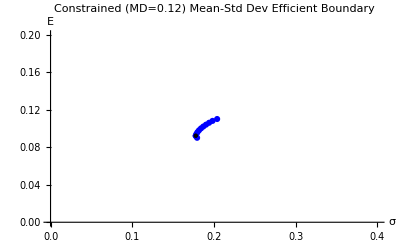
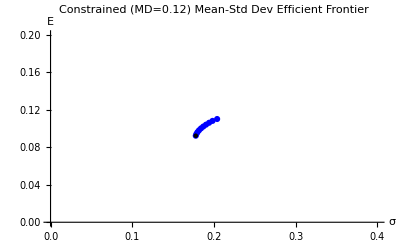

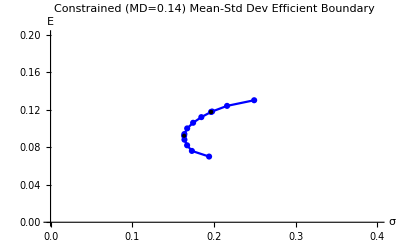
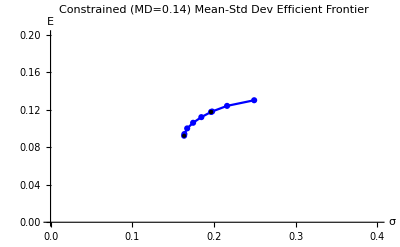

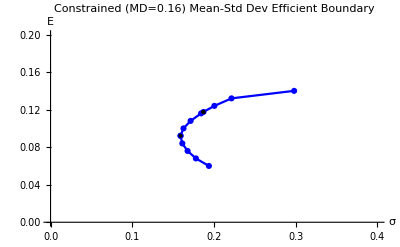
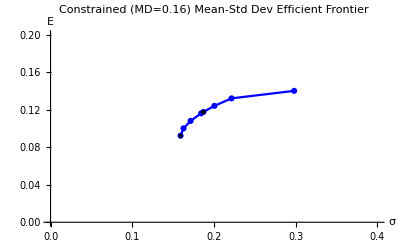

```mathematica
aMVMDResults=<||>;
AppendTo[aMVMDResults,Map[#->xBuildMVMDData[#]&,vMaxDDMVCons]];
Map[Print@aMVMDResults[#][[4]]&,Keys@aMVMDResults];
```

### Mean-Variance Optimization - Unconstrained with Risk Free Security

J = # risky assets     |     r_f = risk free rate     |     w_f = [0  0  0  ...  1]    |    w_t = [ ((Σ^-1(μ-1 r_f))^T)/(a-c r_f) ... 0 ]
θ=(E-E[r_w_t])/(r_f-E[r_w_t])     |     w_E=θw_f+(1-θ)w_t
Risk Free portfolio: w_f, has expected return r_f and variance 0
Tangent Portfolio: w_t, portfolio on the mean-variance boundary without risk free security whose tangent intersects (0, r_f) in  (E[r_w],σ[r_w]) space
A closed-form solution is used to find the Mean-Variance efficient boundary: σ(r_w)=Abs((E[r_w]-r_f)/(√h))     |     h=(μ-1 r_f)^T Σ^-1(μ-1 r_f)

Efficient portfolios on this boundary in (E[r_w],σ[r_w]) space exhibit two-fund separation. The first fund is the risk-free portfolio. The second fund is the tangent portfolio.

The efficient frontier includes the portfolios on this boundary with E[r_w]≥r_f.

#### Parameters and Functions

```mathematica
(*Optimization function. Return standard deviation, expected return and weights of efficient portfolio with given expected return*)
xMVONoConsRF[nEffER_]:=Block[{nWeightθ,nH},
nWeightθ=(nEffER-nTangentPortER)/(nRiskFreeRate-nTangentPortER);
nH=vMeans-vUnit*nRiskFreeRate;
{Abs@((nEffER-nRiskFreeRate)/Sqrt[nH.vvVarCovInvMatrix.nH]),nEffER,nWeightθ*vWeightsRF+(1-nWeightθ)*vWeightsTangent}
]
```

#### Compute and Display Efficient Boundary and Efficient Frontier

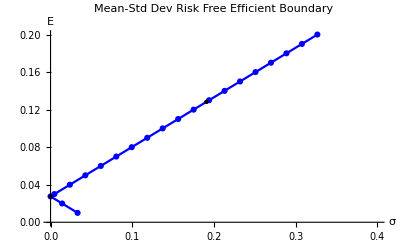
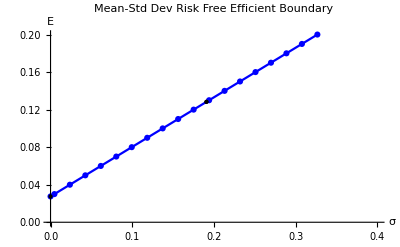

```mathematica
vTangentPort=xMVONoConsRF[nTangentPortER];
vMVRFEffBoundaryPorts=xFeasiblePorts[Join[Table[xMVONoConsRF[nEffER],{nEffER,nMinER,nMaxER,.01}],{vRiskFreePort}]];
vMVRFEffFrontierPorts=Select[vMVRFEffBoundaryPorts,#[[2]]>=vRiskFreePort[[2]]&];

vMVRFEffBoundaryPoints=xMVPoints[vMVRFEffBoundaryPorts,""];
vMVRFEffFrontierPoints=xMVPoints[vMVRFEffFrontierPorts,""];
vMVRFTwoFundPoints=Join[xMVPoints[{vRiskFreePort},"Risk Free Portfolio\n"],xMVPoints[{vTangentPort},"Tangent Portfolio\n"]];

xBoundaryFrontierPlots[
{{vMVRFEffBoundaryPoints},{vMVRFEffFrontierPoints}},
{{vMVRFTwoFundPoints},{vMVRFTwoFundPoints}},
{"Mean-Std Dev Risk Free Efficient Boundary","Mean-Std Dev Risk Free Efficient Boundary"},
{"σ","E"},
{Blue},
{}
]
```

### Mean-Variance Optimization - Maximum Drawdown Constrained with Risk Free Security

w_s_k = [ ((Σ^-1(r_s_k-1 r_f))^T)/(e_s_k-c r_f) ... 0 ]     |     B_(E,D)^((K+1)x1)= [E-r_f  -D-r_f  ...  -D-r_f]     |     R = [μ-1 r_f  r_s_3-1 r_f ...  r_(s_(K+2))-1 r_f]
T=R^T Σ^-1 R     |     [γ_1  γ_3  ...  γ_(K+2)] = T^-1 B_(E,D)     
[θ_1θ_2θ_3... θ_(K+2)] = [1-∑_(k=2)^(K+2) θ_k  γ_1(a-cr_f)  γ_3(e_s_3-cr_f)  ...  γ_(K+2)(e_(s_(K+2))-cr_f)]     |     w_(E,D)=θ_1 w_f+θ_2 w_t+ ∑_(k=3)^(K+2) θ_k w_s_k

A closed-form solution does not exist to find the constrained Mean-Variance efficient boundary. Mathematica’s NMinimize function is capable of solving the vectorized quadratic objective function with 1+S linear constraints. It uses the Nelder-Mead numerical method. 
The program is given as follows: min_(w∈ℝ^J) w^T Σw    
s.t.     w^Tμ-(1-w^T 1) r_f=E, 
	-w^T r_s-(1-w^T 1) r_f≤D  ∀s∈{1,...,S} 
Note that the solution “w” does not include a component for the risk-free security weight. This weight is appended to the vector and equals: 1-∑_(j=1)^J w_j.

Efficient portfolios on this boundary in (E[r_w],σ[r_w]) space exhibit K+2-fund separation. The first two funds w_f and w_t are the same efficient funds from the unconstrained optimization. The remaining K funds are unconstrained mean-variance inefficient funds.

The efficient frontier includes the portfolios on this boundary with E[r_w]≥r_f.

#### Functions

```mathematica
xMVOMDConsRF[nEffER_,nMaxDD_]:=Block[{vWeights,vResult},
vWeights=Table[ToExpression["w"<>ToString@i],{i,iIndexes}];
vResult=NMinimize[{vWeights.vvVarCovMatrix.vWeights,(vWeights.vMeans+(1-vWeights.vUnit)*nRiskFreeRate)==nEffER
&&AllTrue[-vvYearlyReturns.vWeights-(1-vWeights.vUnit)*nRiskFreeRate,#≤nMaxDD&]
},vWeights]//Quiet;
vWeights=vWeights/.vResult[[2]];
{Sqrt[vResult[[1]]],nEffER,Append[vWeights,1-Total@vWeights]}
]

xBuildMVMDRFData[nMaxDD_]:=Block[{vRiskFreePort,vTangentPort,vEffBoundaryPorts,vEffFrontierPorts,nMinER=nMinER,nMaxER=nMaxER,nStepsER=nStepsER,vFundSeps,vEffBoundaryPoints,vEffFrontierPoints,vTwoFundPoints,vFundSepsPoints},

vRiskFreePort=xMVOMDConsRF[nRiskFreeRate,nMaxDD];
vTangentPort=xMVOMDConsRF[nTangentPortER,nMaxDD];

vEffBoundaryPorts=Table[xMVOMDConsRF[nEffER,nMaxDD],{nEffER,nMinER,nMaxER,nStepsER}];
vEffBoundaryPorts=xFeasiblePorts[vEffBoundaryPorts];

If[1<Length@vEffBoundaryPorts<10,
nMinER=Min[vEffBoundaryPorts[[All,2]]];
nMaxER=Max[vEffBoundaryPorts[[All,2]]];
nStepsER=(nMaxER-nMinER)/10;

vEffBoundaryPorts=Table[xMVOMDConsRF[nEffER,nMaxDD],{nEffER,nMinER,nMaxER,nStepsER}];
];

vEffBoundaryPorts=xFeasiblePorts[Join[vEffBoundaryPorts,{vRiskFreePort,vTangentPort}]];
vEffFrontierPorts=Prepend[Select[vEffBoundaryPorts,#[[2]]>vRiskFreePort[[2]]&],vRiskFreePort];

vFundSeps=Map[xMVMDRFFundSeparation[#[[2]],#[[3]],nMaxDD]&,vEffBoundaryPorts];

vEffBoundaryPoints=xMVPoints[vEffBoundaryPorts,""];
vEffFrontierPoints=xMVPoints[vEffFrontierPorts,""];

vTwoFundPoints=Flatten[MapThread[If[0≤#1[[1]]<Infinity,xMVPoints[{#1},#2],Nothing]&,
{{vRiskFreePort,vTangentPort},{"Risk Free Portfolio\n","Tangent Portfolio\n"}}],1];
vFundSepsPoints=xFundSepPoints[vFundSeps];

{vEffBoundaryPoints,vEffFrontierPoints,vTwoFundPoints,
xBoundaryFrontierPlots[
{{vEffBoundaryPoints},{vEffFrontierPoints}},
{{vTwoFundPoints},{vTwoFundPoints}},
{"Constrained (MD="<>ToString@nMaxDD<>") Mean-Std Dev Efficient Boundary","Constrained (MD="<>ToString@nMaxDD<>") Mean-Std Dev Efficient Frontier"},
{"σ","E"},
{Blue},
{}
],
vFundSepsPoints, xFundSepsPlots[vFundSepsPoints,{"Number of Inefficient Funds, MD="<>ToString@nMaxDD,"Sum of Inefficient Fund Weights, MD="<>ToString@nMaxDD},{-12,0}]
}
]

(*Returns: number K of bound states, sum of K inefficient portfolio weights θ, nEffER*)
(*K inefficient MV portfolios given by: xStdDevMean[vF/vE]*)
xMVMDRFFundSeparation[nEffER_,vWeights_,nMaxDD_]:=Block[{vvBoundStates,iBoundStates,vE,vF,vBed,vvR,vvT,vQ,vWeightsθ},
vvBoundStates=MapIndexed[If[#1≤0.001-nMaxDD,{vvYearlyReturns[[First@#2]],First@#2},Nothing]&,vvYearlyReturnsRF.vWeights];
iBoundStates=Length@vvBoundStates;

If[iBoundStates==0,
{0,0,nEffER},

vE=Prepend[Total[vvVarCovInvMatrix].Transpose@vvBoundStates[[All,1]],nA]-nC*nRiskFreeRate;

vBed=Prepend[Table[-nMaxDD,iBoundStates],nEffER]-nRiskFreeRate;
vvR=Prepend[vvBoundStates[[All,1]],vMeans]-nRiskFreeRate;
vvT=vvR.vvVarCovInvMatrix.Transpose@vvR;
vQ=Inverse[vvT].vBed;

vWeightsθ=vQ*vE;

{iBoundStates,Total@vWeightsθ[[2;;]],nEffER}
]
]
```

#### Compute and Display Efficient Boundary and Efficient Frontier for Various MD Levels

You can see that the introduction of the MD constraint decreases the efficient boundary. More discussion in later section.

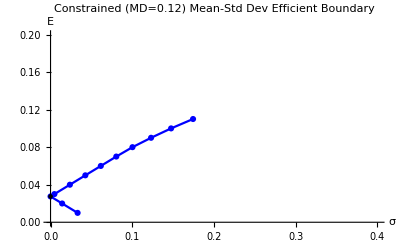
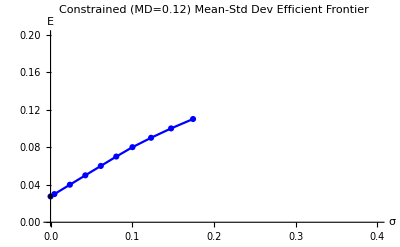

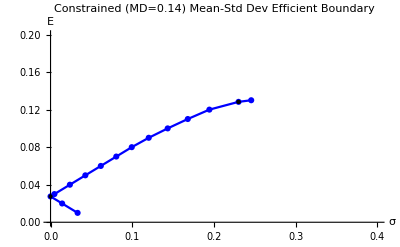
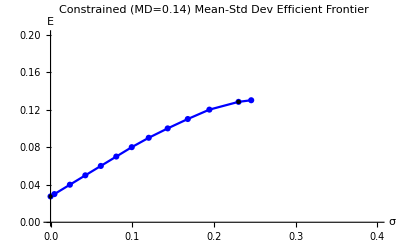

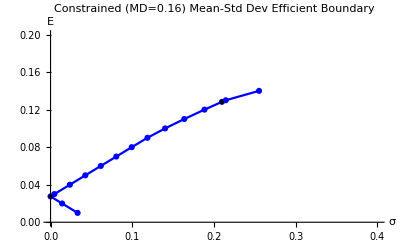
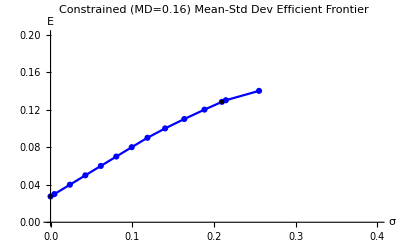

```mathematica
aMVMDRFResults=<||>;
AppendTo[aMVMDRFResults,Map[#->xBuildMVMDRFData[#]&,vMaxDDMVCons]];
Map[Print@aMVMDRFResults[#][[4]]&,Keys@aMVMDRFResults];
```

### Mean-TEV Optimization - Unconstrained without Risk Free Security

w_b= benchmark portfolio weights     |     π=(E-E[r_w_b])/(b/a-a/c)     |     x_E=π(w_a-w_σ)     |     w_E^ϵ=w_b+x_E
Tracking Error Volatility (TEV): σ^ϵ[r_w]=√((w-w_b)^T Σ(w-w_b))

Short sales are allowed, so a closed-form solution exists to find weights for the portfolios on the Mean-TEV efficient boundary. The equations are given above.

Efficient portfolios on this boundary in (E[r_w],TEV[r_w]) space exhibit three-fund separation. The first fund is the benchmark portfolio. The second fund is the minimum variance portfolio. The third fund is the B/A portfolio.

The efficient frontier includes the portfolios on this boundary with E[r_w]≥E[r_w_b].

Efficiency loss (variance units): 0≤η=σ^2[r_w]-1/c+(E[r_w]-a/c)^2/(d/c). This is the difference between the Mean-Variance and Mean-TEV boundaries for a given E[r_w]. When the benchmark portfolio is Mean-Variance efficient, η=0.

#### Parameters and Functions

```mathematica
xMTEVONoConsNoRF[nEffER_]:=Block[{nWeightπ,vWeight},
nWeightπ=(nEffER-nBenchPortER)/(nB/nA-nA/nC);
vWeight=vWeightsBench+nWeightπ*(vWeightsBA-vWeightsσ);
{Sqrt[vWeight.vvVarCovMatrix.vWeight],nEffER,vWeight,Sqrt[(vWeight-vWeightsBench).vvVarCovMatrix.(vWeight-vWeightsBench)]}
]
```

#### Compute and Display Efficient Boundary and Efficient Frontier

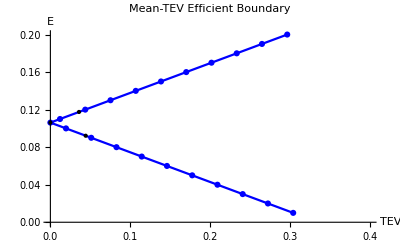
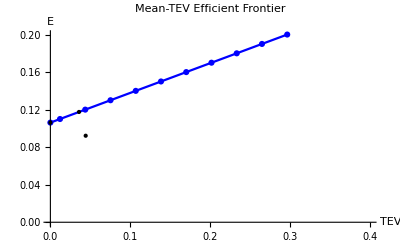

```mathematica
vBenchPort=xMTEVONoConsNoRF[nBenchPortER];  
vMTEVMinVarPort=xMTEVONoConsNoRF[nA/nC];
vMTEVBAPort=xMTEVONoConsNoRF[nB/nA];
vMTEVEffBoundaryPorts=xFeasiblePorts[Join[Table[xMTEVONoConsNoRF[nEffER],{nEffER,nMinER,nMaxER,.01}],{vBenchPort}]];
vMTEVEffMTEVFrontierPorts=Select[vMTEVEffBoundaryPorts,#[[2]]≥vBenchPort[[2]]&];
vMTEVEffMVFrontierPorts=Prepend[Select[vMTEVEffBoundaryPorts,#[[2]]>vMTEVMinVarPort[[2]]&],vMTEVMinVarPort];

vMTEVEffMTEVBoundaryPoints=xMTEVPoints[vMTEVEffBoundaryPorts,""];
vMTEVEffMTEVFrontierPoints=xMTEVPoints[vMTEVEffMTEVFrontierPorts,""];
vMTEVThreeFundMTEVPoints=Join[xMTEVPoints[{vMTEVMinVarPort},"Min Var Portfolio\n"],xMTEVPoints[{vMTEVBAPort},"B/A Portfolio\n"],
xMTEVPoints[{vBenchPort},"Benchmark Portfolio\n"]];

vMTEVEffMVBoundaryPoints= xMVPoints[vMTEVEffBoundaryPorts,""];
vMTEVEffMVFrontierPoints=xMVPoints[vMTEVEffMVFrontierPorts,""];
vMTEVThreeFundMVPoints=Join[xMVPoints[{vMTEVMinVarPort},"Min Var Portfolio\n"],xMVPoints[{vMTEVBAPort},"B/A Portfolio\n"],
xMVPoints[{vBenchPort},"Benchmark Portfolio\n"]];

xBoundaryFrontierPlots[
{{vMTEVEffMTEVBoundaryPoints},{vMTEVEffMTEVFrontierPoints}},
{{vMTEVThreeFundMTEVPoints},{vMTEVThreeFundMTEVPoints}},
{"Mean-TEV Efficient Boundary","Mean-TEV Efficient Frontier"},
{"TEV","E"},
{Blue},
{}
]
```

### Mean-TEV Optimization - Maximum Drawdown Constrained without Risk Free Security

C_(E,D^ϵ)^((K+2)x1) = [0  E-E[r_w_b]  -D^ϵ  ...  -D^ϵ]     |     [δ_1δ_2δ_3... δ_(K+2)] = N^-1 C_(E,D^ϵ)     
[π_1π_2π_3... π_(K+2)] = [δ_1 c  δ_2 a  δ_3 e_s_3... δ_(K+2)e_(s_(K+2))]     |     x_(E,D^ϵ)=π_1 w_σ+π_2 w_a+ ∑_(k=3)^(K+2) π_k w_s_k     |     w_(E,D^ϵ)^ϵ=w_b+x_(E,D^ϵ)
Maximum Tracking Error Drawdown: D^ϵ[r_w]=-(min_(s∈{1,...,S}) (w-w_b))^T r_s

A closed-form solution does not exist to find the constrained Mean-TEV efficient boundary . Mathematica’s NMinimize function is capable of solving the vectorized quadratic objective function with 2+S linear constraints. It uses the Nelder-Mead numerical method. 
The program is given as follows: min_x x^T Σx   
s.t.     x^T1=0, 
	x^T μ =E-E[r_w_b], 
	x^T r_s≤D^ϵ  ∀s∈{1,...,S}
Note that “x” is given above as x_(E,D^ϵ).

Efficient portfolios on this boundary in (E[r_w],TEV[r_w]) space exhibit K+3-fund separation. The first three funds w_b, w_σ and w_a are the same funds from the unconstrained optimization. The remaining K funds are unconstrained Mean-TEV inefficient funds.
The efficient frontier includes the portfolios on this boundary with E[r_w]≥E[r_w_b].

#### Functions

```mathematica
xMTEVOMDConsNoRF[nEffER_,nMaxDD_]:=Block[{vWeights,vResult},
vWeights=Table[ToExpression["w"<>ToString@i],{i,iIndexes}];
vResult=NMinimize[{vWeights.vvVarCovMatrix.vWeights,vWeights.vUnit==0&&vWeights.vMeans==(nEffER-nBenchPortER)&&AllTrue[-vvYearlyReturns.vWeights,#≤nMaxDD&]
},vWeights]//Quiet;

vWeights=(vWeights/.vResult[[2]]) + vWeightsBench;
{If[vResult[[1]]==Infinity,Infinity,Sqrt[vWeights.vvVarCovMatrix.vWeights]],nEffER,vWeights,Sqrt[vResult[[1]]]}
]

xBuildMTEVMDData[nMaxDD_]:=Block[{vMinVarPort,vBAPort,vBenchPort,vEffBoundaryPorts,vEffFrontierPorts,nMinER=nMinER,nMaxER=nMaxER,nStepsER=nStepsER, vFundSeps,vEffBoundaryPoints,vEffFrontierPoints,vThreeFundPoints,vFundSepsPoints,vEffMVBoundaryPoints,vEffMVFrontierPoints,vMVThreeFundPoints},

vMinVarPort=xMTEVOMDConsNoRF[nA/nC,nMaxDD];
vBAPort=xMTEVOMDConsNoRF[nB/nA,nMaxDD];
vBenchPort=xMTEVOMDConsNoRF[nBenchPortER,nMaxDD];

vEffBoundaryPorts=Table[xMTEVOMDConsNoRF[nEffER,nMaxDD],{nEffER,nMinER,nMaxER,nStepsER}];
vEffBoundaryPorts=xFeasiblePorts[vEffBoundaryPorts];

If[1<Length@vEffBoundaryPorts<10,
nMinER=Min[vEffBoundaryPorts[[All,2]]];
nMaxER=Max[vEffBoundaryPorts[[All,2]]];
nStepsER=(nMaxER-nMinER)/10;

vEffBoundaryPorts=Table[xMTEVOMDConsNoRF[nEffER,nMaxDD],{nEffER,nMinER,nMaxER,nStepsER}];
];
vEffBoundaryPorts=xFeasiblePorts[Join[vEffBoundaryPorts,{vMinVarPort,vBAPort,vBenchPort}]];
vEffFrontierPorts=Prepend[Select[vEffBoundaryPorts,#[[2]]>vBenchPort[[2]]&],vBenchPort];

vFundSeps=Map[xMTEVMDFundSeparation[#[[2]],#[[3]],nMaxDD]&,vEffBoundaryPorts];

vEffBoundaryPoints=xMTEVPoints[vEffBoundaryPorts,""];
vEffFrontierPoints=xMTEVPoints[vEffFrontierPorts,""];
vThreeFundPoints=Flatten[MapThread[If[0≤#1[[4]]<Infinity,xMTEVPoints[{#1},#2],Nothing]&,
{{vMinVarPort,vBAPort,vBenchPort},{"Min Var Portfolio\n","B/A Portfolio\n","Benchmark Portfolio\n"}}],1];
vFundSepsPoints=xFundSepPoints[vFundSeps];

vEffMVBoundaryPoints=xMVPoints[vEffBoundaryPorts,""];
vEffMVFrontierPoints=xMVPoints[vEffFrontierPorts,""];
vMVThreeFundPoints=Flatten[MapThread[If[0≤#1[[2]]<Infinity,xMVPoints[{#1},#2],Nothing]&,
{{vMinVarPort,vBAPort,vBenchPort},{"Min Var Portfolio\n","B/A Portfolio\n","Benchmark Portfolio\n"}}],1];

{vEffBoundaryPoints,vEffFrontierPoints,vThreeFundPoints,
xBoundaryFrontierPlots[
{{vEffBoundaryPoints},{vEffFrontierPoints}},
{{vThreeFundPoints},{vThreeFundPoints}},
{"Constrained (MD="<>ToString@nMaxDD<>") Mean-TEV Efficient Boundary","Constrained (MD="<>ToString@nMaxDD<>") Mean-TEV Efficient Frontier"},
{"TEV","E"},
{Blue},
{}
],
vFundSepsPoints, xFundSepsPlots[vFundSepsPoints,{"Number of Inefficient Funds, MD="<>ToString@nMaxDD,"Sum of Inefficient Fund Weights, MD="<>ToString@nMaxDD},{0,2}],
vEffMVBoundaryPoints,vEffMVFrontierPoints,vMVThreeFundPoints
}
]

(*Returns: number K of bound states, sum of K inefficient portfolio weights π, nEffER*)
xMTEVMDFundSeparation[nEffER_,vWeights_,nMaxDD_]:=Block[{vvBoundStates,iBoundStates,vE,vF,vCed,vvMTrans,vvN,vWeightsπ},
vvBoundStates=MapIndexed[If[#1≤0.001-nMaxDD,{vvYearlyReturns[[First@#2]],First@#2},Nothing]&,vvYearlyReturns.(vWeights-vWeightsBench)];
iBoundStates=Length@vvBoundStates;

If[iBoundStates==0,
{0,0,nEffER},

vF=Transpose@(vvVarCovInvMatrix.(Transpose@vvBoundStates[[All,1]]));
vE=vF.vUnit;

vCed=Join[{0,nEffER-nBenchPortER},Table[-nMaxDD,iBoundStates]];
vvMTrans=Join[{vUnit,vMeans},vvBoundStates[[All,1]]];
vvN=vvMTrans.vvVarCovInvMatrix.(Transpose@vvMTrans);
vWeightsπ=(Inverse[vvN].vCed)*Join[{nC,nA},vE];

{iBoundStates,Total@vWeightsπ[[3;;]],nEffER}
]
]
```

#### Compute and Display Efficient Boundary and Efficient Frontier for Various MD Levels

You can see that the introduction of the MD constraint decreases the efficient boundary.

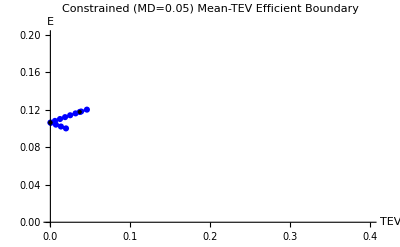
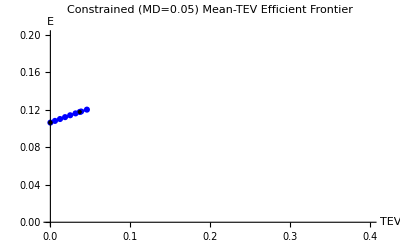

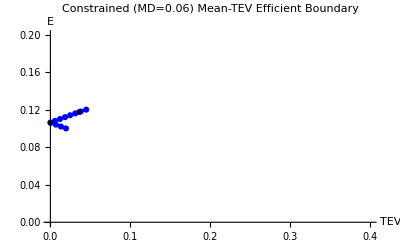
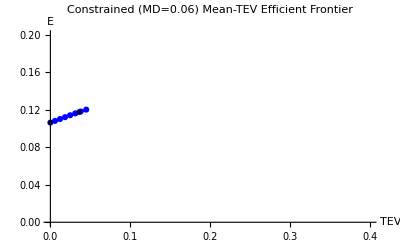

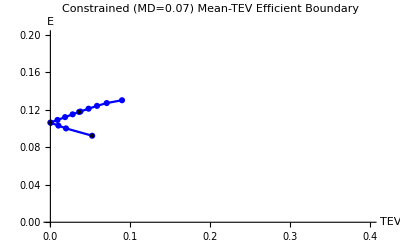
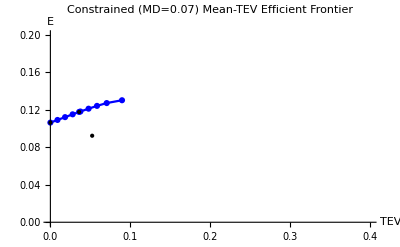

```mathematica
aMTEVMDResults=<||>;
AppendTo[aMTEVMDResults,Map[#->xBuildMTEVMDData[#]&,vMaxDDMTEVCons]];
Map[Print@aMTEVMDResults[#][[4]]&,Keys@aMTEVMDResults];
```

## Analysis of Results

### Mean-Std Dev Efficient Boundary and Frontier for Three Unconstrained Optimizations

These graphs show the (σ,E) efficient boundary order for the following: MV RF (Red) ≤ MV No RF (Blue) ≤ MTEV No RF (Green) for all E.
If the benchmark portfolio is Mean-Variance No RF efficient, then the entire Mean-TEV boundary is Mean-Variance No RF efficient.
The black dots are the special portfolios (mentioned previously) that characterize each efficient boundary.

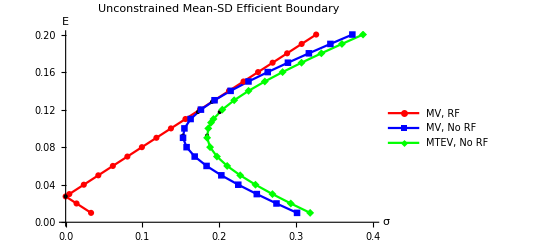
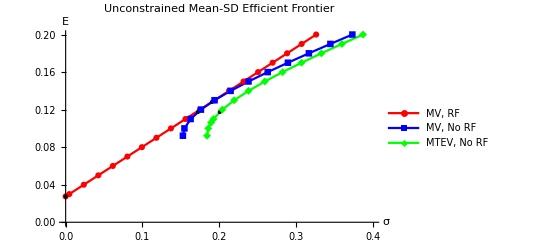

```mathematica
xBoundaryFrontierPlots[
{{vMVRFEffBoundaryPoints,vMVEffBoundaryPoints,vMTEVEffMVBoundaryPoints},{vMVRFEffFrontierPoints,vMVEffFrontierPoints,vMTEVEffMVFrontierPoints}},
{Join[vMVTwoFundPoints,vMVRFTwoFundPoints,vMTEVThreeFundMVPoints],{Join[vMVTwoFundPoints,vMVRFTwoFundPoints,vMTEVThreeFundMVPoints]}},
{"Unconstrained Mean-SD Efficient Boundary","Unconstrained Mean-SD Efficient Frontier"},
{"σ","E"},
{Red,Blue,Green},
{"MV, RF","MV, No RF","MTEV, No RF"}
]
```

### Analysis of Mean-Variance Optimization without Risk Free Security

#### Mean-SD Plots of Unconstrained and MD Constrained Efficient Boundary and Frontier For Three MD Constraints

The addition of a MD constraint moves the efficient boundary to the right. So, constrained portfolios are inefficient with respect to the unconstrained boundary.
Decreasing the MD constraint too much (e.g. to .1) yields no feasible portfolios. 
Increasing the MD constraint allows for the boundary to include a wider range of expected returns. 
Increasing the MD constraint enough (depending on data) will yield the unconstrained efficient boundary.
Expected returns at the higher and lower end of the feasible range require relatively higher SD to meet the MD constraint. 
It appears that the unconstrained minimum variance portfolio is also the constrained minimum variance portfolio.

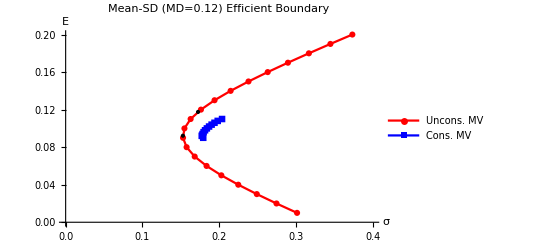
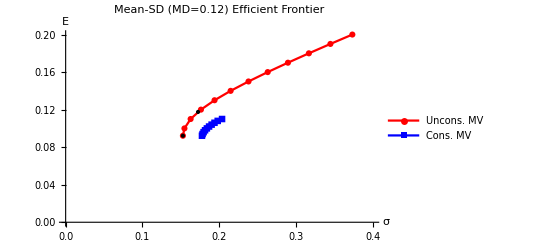

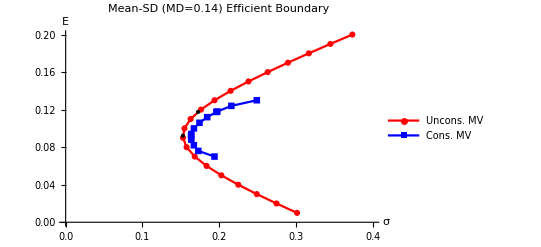
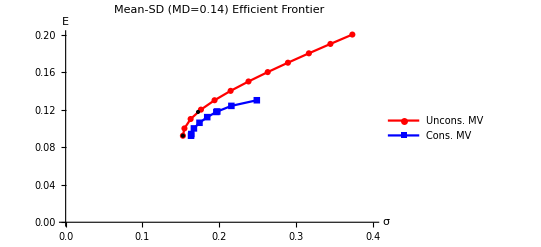

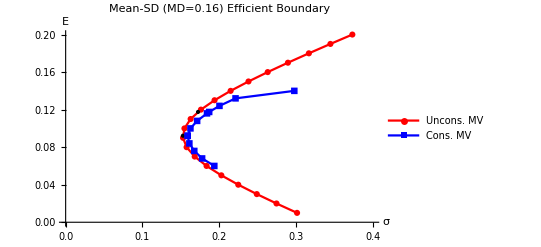
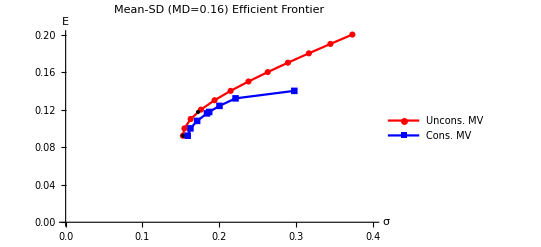

```mathematica
Map[Print@xBoundaryFrontierPlots[
{{vMVEffBoundaryPoints,(aMVMDResults[#])[[1]]},{vMVEffFrontierPoints,(aMVMDResults[#])[[2]]}},
{Join[vMVTwoFundPoints,(aMVMDResults[#])[[3]]],Join[vMVTwoFundPoints,(aMVMDResults[#])[[3]]]},
{"Mean-SD (MD="<>ToString@#<>") Efficient Boundary","Mean-SD (MD="<>ToString@#<>") Efficient Frontier"},
{"σ","E"},
{Red,Blue},
{"Uncons. MV","Cons. MV"}
]&,vMaxDDMVCons];
```

#### Plots of Expected Return vs. Number of Inefficient Funds and Sum of Inefficient Fund Weights

Refer to the previous section “Mean-Variance Optimization - Maximum Drawdown Constrained without Risk Free Security”.
A bound state is any state where the negative of the portfolio’s return equals the MD constraint.
Portfolios w_(E,D) on the MD constrained Mean-SD efficient boundary have K+2 fund separation. In other words, w_(E,D) is a linear combination K+2 funds. 
K is the number of bound states. K of the funds are unconstrained MV inefficient and 2 are unconstrained MV efficient. 
As noted previously, as the MD constraint increases, the range of feasible expected returns increases.
Efficient portfolios close to the max and min of the feasible expected return range have higher fund separation: they are combinations of more inefficient funds with higher (negative) weights. 
As the MD constraint increases, the fund separation of efficient portfolios decreases: they are combinations of a fewer inefficient funds with lower (negative) weights. 
The sum of the inefficient fund is parabolic and appears to be minimized near the minimum variance portfolio.
Fewer inefficient funds does not guarantee a smaller sum of inefficient fund weights. 
In these 3 cases, there are never more than 8 inefficient funds, though the sum of their weights can differ greatly.

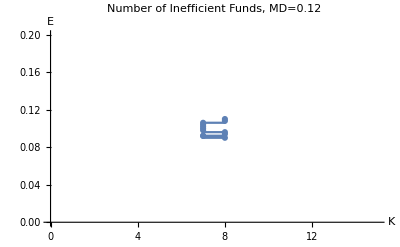
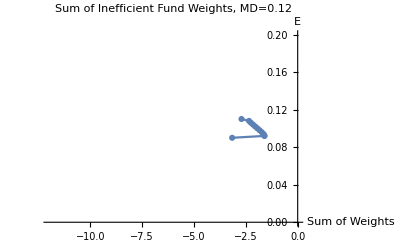

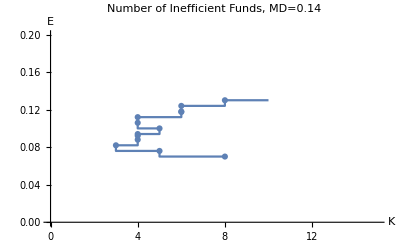
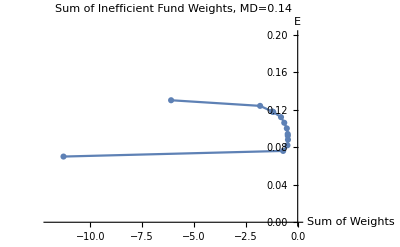

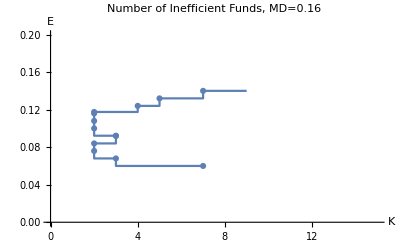
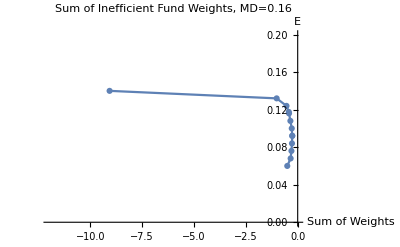

```mathematica
Map[Print@aMVMDResults[#][[6]]&,Keys@aMVMDResults];
```

### Analysis of Mean-Variance Optimization with Risk Free Security

#### Mean-SD Plots of Unconstrained and MD Constrained Efficient Boundary and Frontier For Three MD Constraints

The addition of a MD constraint moves the efficient boundary to the right for higher expected returns.
So, constrained portfolios are inefficient with respect to the unconstrained boundary.
However, the shift is much less pronounced here than on the No RF efficient boundary. 
The addition of a MD constraint does not move the efficient boundary for lower expected returns.
Due to the risk free asset, feasible portfolios exist for all MD constraints ≥ 0
Increasing the MD constraint allows for the boundary to include a wider range of expected returns. 
Increasing the MD constraint enough (depending on data) will yield the unconstrained efficient boundary.
Expected returns at the higher end of the feasible range require relatively higher SD to meet the MD constraint.

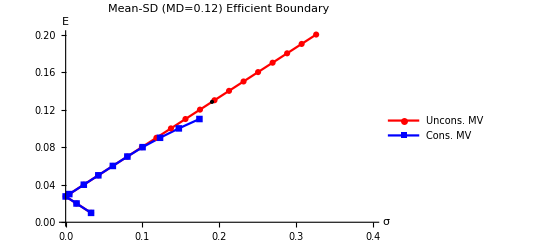
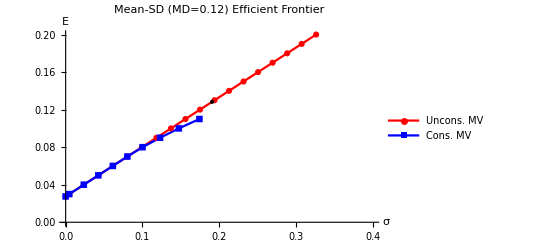

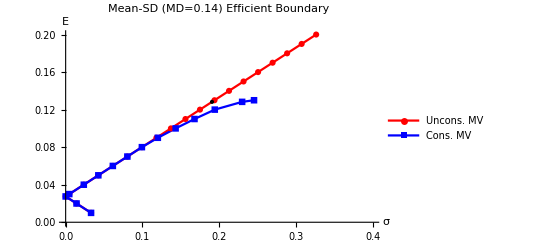
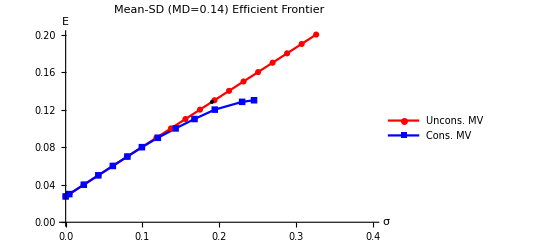

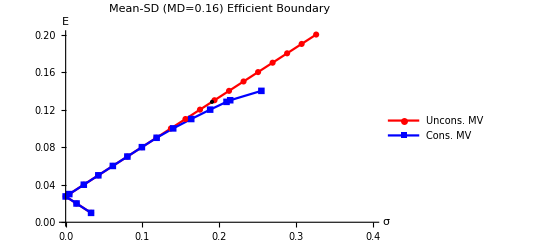
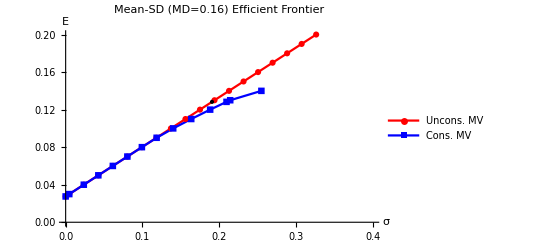

```mathematica
Map[Print@xBoundaryFrontierPlots[
{{vMVRFEffBoundaryPoints,(aMVMDRFResults[#])[[1]]},{vMVRFEffFrontierPoints,(aMVMDRFResults[#])[[2]]}},
{Join[vMVRFTwoFundPoints,(aMVMDRFResults[#])[[3]]],Join[vMVRFTwoFundPoints,(aMVMDRFResults[#])[[3]]]},
{"Mean-SD (MD="<>ToString@#<>") Efficient Boundary","Mean-SD (MD="<>ToString@#<>") Efficient Frontier"},
{"σ","E"},
{Red,Blue},
{"Uncons. MV","Cons. MV"}
]&,vMaxDDMVCons];
```

#### Plots of Expected Return vs. Number of Inefficient Funds and Sum of Inefficient Fund Weights

Refer to the previous section “Mean-Variance Optimization - Maximum Drawdown Constrained with Risk Free Security”.
Portfolios w_(E,D) on the MD constrained Mean-SD efficient boundary have K+2 fund separation. In other words, w_(E,D) is a linear combination K+2 funds. 
K is the number of bound states. K of the funds are unconstrained MV inefficient and 2 are unconstrained MV efficient. 
As noted previously, as the MD constraint increases, the range of feasible expected returns increases. Since the risk free rate is close to 0, this is only apparent for higher expected returns.
Efficient portfolios close to the max of the feasible expected return range have higher fund separation: they are combinations of more inefficient funds with higher (negative) weights. 
As the MD constraint increases, the fund separation of efficient portfolios decreases: they are combinations of a fewer inefficient funds with lower (negative) weights. 
Lower expected returns are characterized completely by the risk free and tangent portfolios. The number of these portfolios increases as the MD constraint increases.
It appears that as the number of inefficient funds increases, the sum of their weights also increases. 
In these 3 cases, there are never more than 8 inefficient funds, though the sum of their weights can differ greatly.

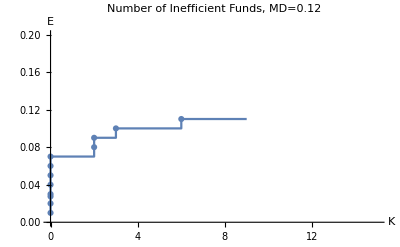
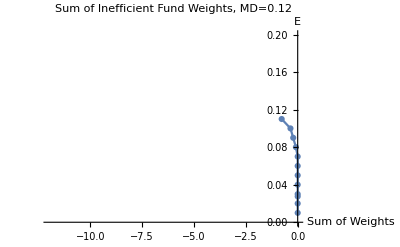

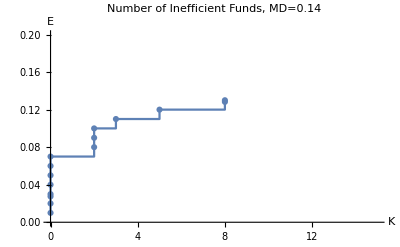
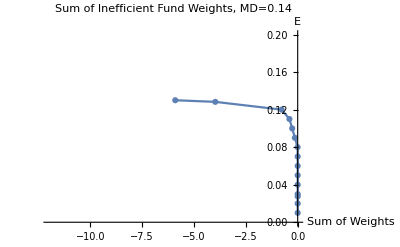

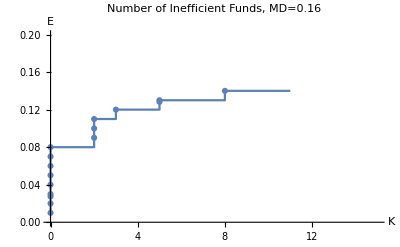
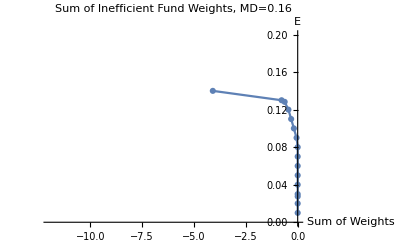

```mathematica
Map[Print@aMVMDRFResults[#][[6]]&,Keys@aMVMDResults];
```

### Analysis of Mean-TEV Optimization without Risk Free Security

#### Mean-TEV Plots of Unconstrained and MD Constrained Efficient Boundary and Frontier For Three MD Constraints

The Mean-TEV efficient boundary is 2-piece linear, unlike the MV efficient boundary. 
The addition of a MD constraint moves the efficient boundary to the right for expected returns closer to the max and min of the feasible expected return range.
So, these constrained portfolios are inefficient with respect to the unconstrained boundary.
The addition of a MD constraint does not move the efficient boundary for expected returns closer to the center of the feasible expected return range.
However, the shift is much less pronounced here than on the MV No RF efficient boundary.
Due to the benchmark portfolio, feasible portfolios exist for all MD constraints ≥ 0
However, decreasing the MD constraint too much (e.g. to .01) will yield practically no other feasible portfolios. 
Increasing the MD constraint allows for the boundary to include a wider range of expected returns. 
Increasing the MD constraint enough (depending on data) will yield the unconstrained efficient boundary.
Expected returns at the higher and lower end of the feasible range require relatively higher TEV to meet the MD constraint. 
Depending on the benchmark choice, the minimum variance portfolio and the B/A portfolio may or may not be on the efficient frontier.

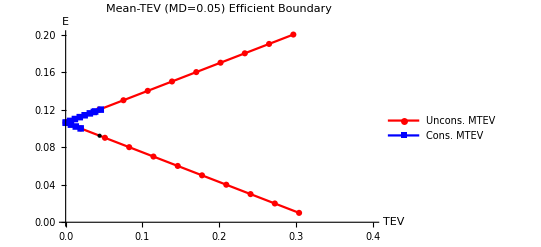
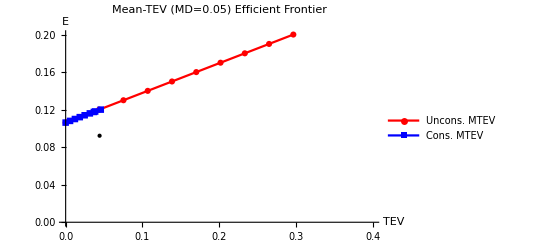

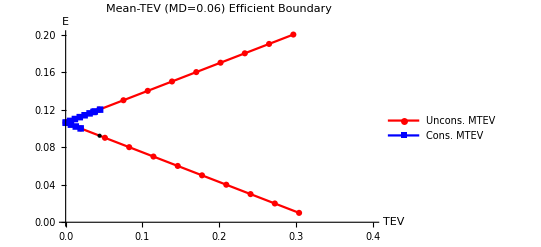
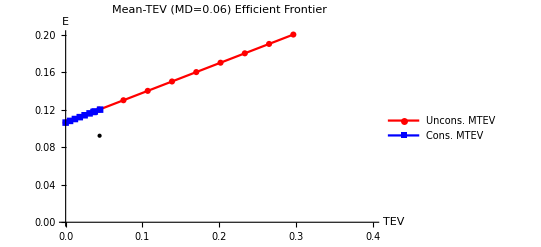

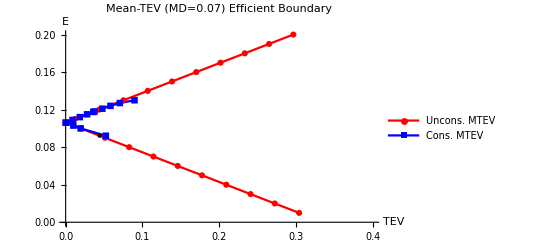
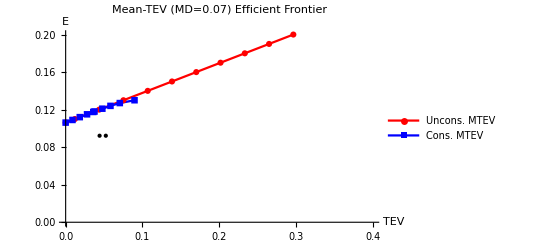

-Graphics-           -Graphics-

-Graphics-           -Graphics-

```mathematica
Map[Print@xBoundaryFrontierPlots[
{{vMTEVEffMTEVBoundaryPoints,(aMTEVMDResults[#])[[1]]},{vMTEVEffMTEVFrontierPoints,(aMTEVMDResults[#])[[2]]}},
{Join[vMTEVThreeFundMTEVPoints,(aMTEVMDResults[#])[[3]]],Join[vMTEVThreeFundMTEVPoints,(aMTEVMDResults[#])[[3]]]},
{"Mean-TEV (MD="<>ToString@#<>") Efficient Boundary","Mean-TEV (MD="<>ToString@#<>") Efficient Frontier"},
{"TEV","E"},
{Red,Blue},
{"Uncons. MTEV","Cons. MTEV"}
]&,vMaxDDMTEVCons];
```

#### Mean-SD Plots of Unconstrained Mean-Variance, Mean-TEV, and MD Constrained Mean-TEV Efficient Boundary and Frontier For Three MD Constraints

The Mean-SD efficient boundary is in red. The Mean-TEV efficient boundary (blue) and MD constrained Mean-TEV efficient boundary (green) are both Mean-SD inefficient.

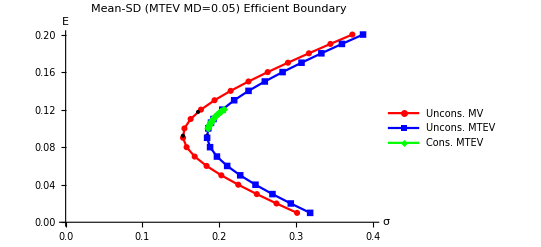
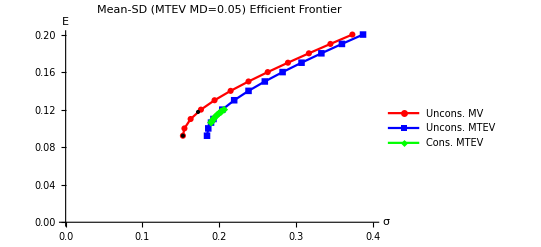

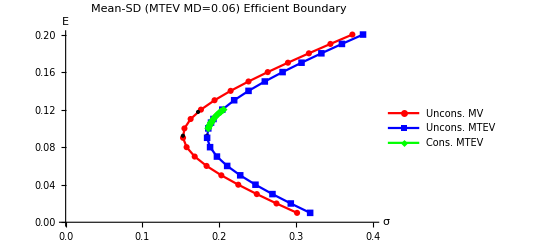
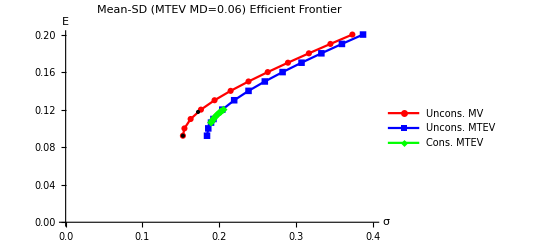

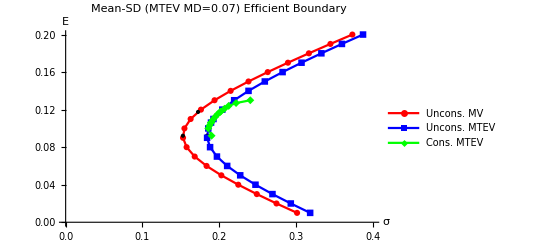
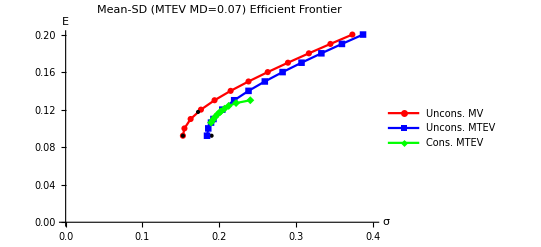

```mathematica
Map[Print@xBoundaryFrontierPlots[
{{vMVEffBoundaryPoints,vMTEVEffMVBoundaryPoints,aMTEVMDResults[#][[7]]},{vMVEffFrontierPoints,vMTEVEffMVFrontierPoints,aMTEVMDResults[#][[8]]}},
{Join[vMVTwoFundPoints,vMTEVThreeFundMVPoints,aMTEVMDResults[#][[9]]],Join[vMVTwoFundPoints,vMTEVThreeFundMVPoints,aMTEVMDResults[#][[9]]]},
{"Mean-SD (MTEV MD="<>ToString@#<>") Efficient Boundary","Mean-SD (MTEV MD="<>ToString@#<>") Efficient Frontier"},
{"σ","E"},
{Red,Blue,Green},
{"Uncons. MV","Uncons. MTEV","Cons. MTEV"}
]&,vMaxDDMTEVCons];
```

#### Plots of Expected Return vs. Number of Inefficient Funds and Sum of Inefficient Fund Weights

Refer to the previous section “Mean-TEV Optimization - Maximum Drawdown Constrained without Risk Free Security”.
Portfolios w_(E,D^ϵ)^ϵ on the MD constrained Mean-TEV efficient boundary have K+3 fund separation. In other words, w_(E,D^ϵ)^ϵ is a linear combination K+3 funds. 
K is the number of bound states. K of the funds are unconstrained MTEV inefficient and 3 are unconstrained MTEV efficient. 
As noted previously, as the MD constraint increases, the range of feasible expected returns increases. 
Efficient portfolios close to the max and min of the feasible expected return range have higher fund separation: they are combinations of more inefficient funds with higher weights. 
As the MD constraint increases, the fund separation of efficient portfolios decreases: they are combinations of a fewer inefficient funds with lower weights. 
It appears that as the number of inefficient funds increases, the sum of their weights also increases. 
In these 3 cases, there are never more than 8 inefficient funds, though the sum of their weights can differ greatly.
Increasing the MD constraint from 0.05 to 0.06 marginally increases the range of expected returns (by <0.01), but it does decrease the fund separation for funds in that range, as expected.

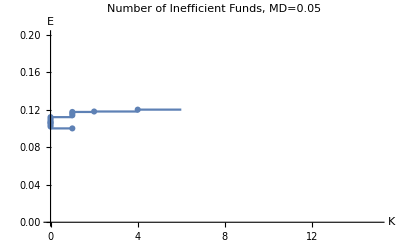
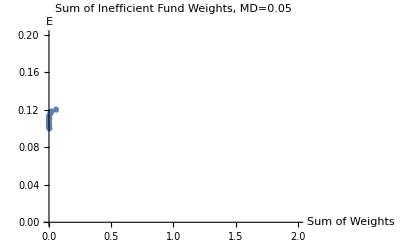

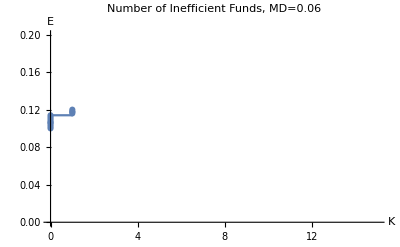
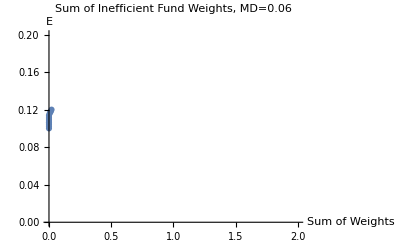

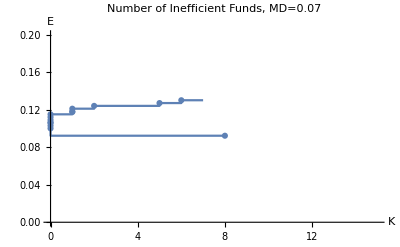
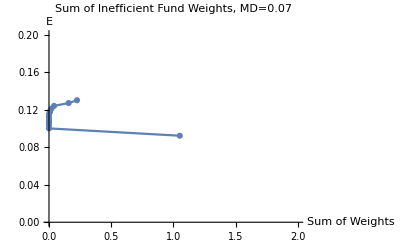

```mathematica
Map[Print@aMTEVMDResults[#][[6]]&,Keys@aMTEVMDResults];
```

### Issues Encountered and Other Concerns

1. The data were gathered from the same source but the source data has changed. This is shown with the mean, SD and correlation tables. So, our results are similar to the paper but not quite the same.

2. Matrix Inversion issues: Mathematica gave warnings about badly conditioned matrices, but it is not clear from our results if this had any effect.

3. Numerical issues: We originally used a minimum function for the maximum drawdown constraint in the NMinimize optimization functions. This had little effect in both Mean-Variance optimizations. However, the Mean-TEV optimization was taking ~10 minutes to complete for low maximum drawdown constraints (e.g. 0.05 and 0.06) and was providing erroneous results. For example, a solution for the portfolio with expected return a/c (minimum variance portfolio) was found for 0.06 max drawdown but not at 0.07. We replaced the minimum function with linear inequalities and the run time dropped to a few seconds and provided correct results.

4. The implementation of the utility function U(E,σ)=E-ρ/2 σ^2 is not discussed in the paper, but other papers are referenced. The results from choosing different values of ρ are discussed.